# FAQ : Indexed Concatenation

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

An Indexed Concatenation is a mathematical notation designed to represent complex datasets in a more concise form. This is typically done by combining repeated elements of the dataset to create a more compact list.

### Basics of using Indexed Concatenation to summarize a network.

Here is the example graph used in the SIMULTECH2025 Paper, to be presented by Rhys Sharpe in June 2025, in Bilbao, Spain. Clear patterns are visible:

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
EDSL1={{1,1,2,2},{2,2},{2,4},{1,5},{1,1},{1,10},{1,10},{},{1,1,2,2},{2,2},{2,4},{1,7},{1,1},{1,12},{1,12},{1,12},{1,12},{},{1,1,2,2},{2,2},{2,4},{1,9},{1,1},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{},{1,1,2,2},{2,2},{2,4},{1,11},{1,1},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{},{1,1,2,2},{2,2},{2,4},{1,13},{1,1},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{},{1,1,2,2},{2,2},{2,4},{1,15},{1,1},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{},{1,1,2,2},{2,2},{2,4},{1,17},{1,1},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{},{1,1,2,2},{2,2},{2,4},{1,19},{1,1},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{},{1,1,2,2},{2,2},{2,4},{1,21},{1,1},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{},{1,1,2,2},{2,2},{2,4},{1,23},{1,1},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{},{1,1,2,2},{2,2},{2,4},{1,25},{1,1},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{},{1,1,2,2},{2,2},{2,4},{1,27},{1,1},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{},{1,1,2,2},{2,2},{2,4},{1,29},{1,1},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{},{1,1,2,2},{2,2},{2,4},{1,31},{1,1},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{},{1,1,2,2},{2,2},{2,4},{1,33},{1,1},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{},{1,1,2,2},{2,2},{2,4},{1,35},{1,1},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{},{1,1,2,2},{2,2},{2,4},{1,37},{1,1},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{},{1,1,2,2},{2,2},{2,4},{1,39},{1,1},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{1,44},{}};
Net1=FromNetDifferenceSets[EDSL1];
IC1=
{IndexedConcatenate[{1,1,2,2},
IndexedConcatenate[{2,2j},{j,1,2}],
{1,3+2*k},{1,1},IndexedConcatenate[{1,8+2 k},{i,1,2k}],{},{k,1,18}]};
Net1[[1;;100]]
```

{1→2,1→2,1→3,1→3,2→4,2→4,3→5,3→7,4→5,4→9,5→6,5→6,6→7,6→16,7→8,7→17,9→10,9→10,9→11,9→11,10→12,10→12,11→13,11→15,12→13,12→19,13→14,13→14,14→15,14→26,15→16,15→27,16→17,16→28,17→18,17→29,19→20,19→20,19→21,19→21,20→22,20→22,21→23,21→25,22→23,22→31,23→24,23→24,24→25,24→38,25→26,25→39,26→27,26→40,27→28,27→41,28→29,28→42,29→30,29→43,31→32,31→32,31→33,31→33,32→34,32→34,33→35,33→37,34→35,34→45,35→36,35→36,36→37,36→52,37→38,37→53,38→39,38→54,39→40,39→55,40→41,40→56,41→42,41→57,42→43,42→58,43→44,43→59,45→46,45→46,45→47,45→47,46→48,46→48,47→49,47→51,48→49,48→61,49→50,49→50}

The data listed above represents the first 100 edges of the graph. 1 -> 2 means a connection between vertices 1 and 2.  We note that the repetitive patterns in the graph are not at all visible in the edge list. But grouping edges by “out-vertex” and taking the differences of the vertex numbers for each edge gives the edge difference set list (EDSL), in which patterns reappear.

This shows how the graph edges correspond to sets in the EDSL. Even in the first few sets we begin to see some repetitions:

```mathematica
Grid[{
{"Edges:"}~Concatenate~Insert[GatherBy[Net1[[1;;20]],First],{},8]~Concatenate~{"…"},
{"EDSL:"}~Concatenate~EDSL1[[1;;9]]~Concatenate~{"…"}
}, Alignment->Left, Dividers->All]
```

Edges: | {1→2,1→2,1→3,1→3} | {2→4,2→4} | {3→5,3→7} | {4→5,4→9} | {5→6,5→6} | {6→7,6→16} | {7→8,7→17} | {} | {9→10,9→10,9→11,9→11} | …
EDSL: | {1,1,2,2} | {2,2} | {2,4} | {1,5} | {1,1} | {1,10} | {1,10} | {} | {1,1,2,2} | …

For this graph, the first 100 entries in the EDSL are given below. Runs of duplicates are highlighted:

```mathematica
EDSL1[[1;;100]]
```

```mathematica
{{1,1,2,2},{2,2},{2,4},{1,5},{1,1},{1,10},{1,10},{},{1,1,2,2},{2,2},{2,4},{1,7},{1,1},{1,12},{1,12},{1,12},{1,12},{},{1,1,2,2},{2,2},{2,4},{1,9},{1,1},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{},{1,1,2,2},{2,2},{2,4},{1,11},{1,1},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{},{1,1,2,2},{2,2},{2,4},{1,13},{1,1},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{},{1,1,2,2},{2,2},{2,4},{1,15},{1,1},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{},{1,1,2,2},{2,2},{2,4},{1,17},{1,1},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{},{1,1,2,2},{2,2}}
```

An EDSL of a network having some intrinsic pattern typically contains some duplicate sets, which provides an obvious first step in condensing the network down. In this EDSL we see 2 adjacent copies of {1,10}, 4 adjacent copies of {1,12}, 6 copies of {1,14}, 8 copies of {1,16}, etc., which we  represent €^2[{1,10}], €^4[{1,12}], €^6[{1,14}], €^8[{1,16}], etc. By reducing the graph down like this, we can notice further patterns. Here is the EDSL above, separated onto different lines to showcase the next step.

{1, 1, 2, 2}, {2, 2}, {2, 4}, {1, 5}, {1, 1}, €^2[{1, 10}], {},
    {1, 1, 2, 2}, {2, 2}, {2, 4}, {1, 7}, {1, 1}, €^4{1, 12}], {},
    {1, 1, 2, 2}, {2, 2}, {2, 4}, {1, 9}, {1, 1}, €^6[{1, 14}], {},
    {1, 1, 2, 2}, {2, 2}, {2, 4},{1, 11},{1, 1},€^8[{1, 16}], {}, …

After we do this, there is no further reduction that can be done based on exact duplicates of adjacent sets, but we can see that each 7-element row has a common pattern, with only 3 numbers changing in each row. In the first row these numbers are 5, 2, and 10; and in the second row these numbers are 7, 4, and 12; and in general, in the k^th row, they are 2k + 3, 2k, and 2k+8. Before moving on to the details of the Indexed Concatenation Notation, the fully reduced EDSL is listed below.

```mathematica
IC1
```

{€_(k⊨1)^18[{1,1,2,2},€_(j⊨1)^2[{2,2 j}],{1,3+2 k},{1,1},€_(i⊨1)^(2 k)[{1,8+2 k}],{}]}

Note that index variables, i, j, and k, have been introduced. Just as one would expect by analogy to an indexed summation, i, j, and k take on the initial value of 1 and are incremented until the specified final values are reached. In this case it’s 2k, 2 and 18, but the latter can be replaced by ∞. Assuming the pattern has been well established and will continue indefinitely, we have succeeded in summarizing the entire infinite network’s EDSL in one line! Similarly, most causal networks generated by a Sessie (Sequential Substitution System) Ruleset can be summarized by this notation.

### Some other examples of I-CATs of networks

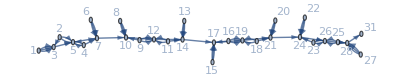

{€^4[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3}]}

```mathematica
(* sssNB2=SSS[{"AAAAB"->"B",""->"AAA"},"B",52,SSSMax->25,NetMax->28,NetSize->550,DirectedEdges->True];
ReduceSetList[ToNetDifferenceSets@sssNB2[["Net"]]];
%[[1;;-3]]//InputForm; *)

ICNB2={IndexedConcatenate[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3},4]};
Graph[FromNetDifferenceSets[ExpandAll[ICNB2]],VertexLabels->"Name",GraphLayout->"SpringElectricalEmbedding"]
Style[ICNB2,"DisplayFormula"]
```

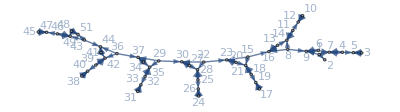

{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}

```mathematica
(* sssNB4=SSS[{"AAABA"->"",""->"AABA"},"",50,SSSMax->25,NetSize->550,DirectedEdges->True];
ReduceSetList[ToNetDifferenceSets@sssNB4[["Net"]]]
%[[2;;2]]//InputForm *)

ICNB4={IndexedConcatenate[{1, 6, 8}, {}, {IndexedConcatenate[2,4]}, IndexedConcatenate[{1, IndexedConcatenate[3,3]}, {}, 2], 7]};
Graph[FromNetDifferenceSets[ExpandAll[ICNB4]],VertexLabels->"Name",GraphLayout->"SpringElectricalEmbedding"]
Style[ICNB4,"DisplayFormula"]
```

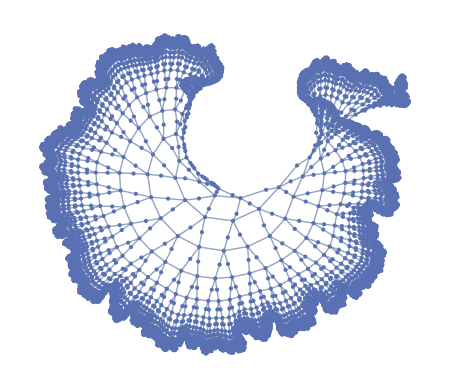

{€_(k⊨1)^10[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]}

```mathematica
IC2j={IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k}, 1 + 2^k], {1}, 
 IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 10}]};
Graph[FromNetDifferenceSets[ExpandAll[IC2j]],VertexLabels->None,DirectedEdges->False,ImageSize->450]
Style[IC2j,"DisplayFormula"]
```

### Examples of I-CATs summarizing patterns in decimal expansions:

```mathematica
Grid[{
{"Fraction","Decimal Representation","Indexed Concatenation","Summation"},
{"1/3","0.33333…",Row[{"0.",€^∞,"3"}],"0+∑_(k = 1)^∞ (3·10^-k)"},
{"1/9","0.1111111111…",Row[{"0.",€^∞,"1"}],"0+∑_(k = 1)^∞ (1·10^-k)"},
{"1/11","0.0909090909…",Row[{"0.",€^∞,"09"}],"0+∑_(k = 1)^∞ (9·10^-k)"},
{"1/7","0.14285714285714285714…",Row[{"0.",€^∞,"142857"}],"0+∑_(k = 1)^∞ (1428571·10^(-6 k))"},
{"1/13","0.076923076923076923…",Row[{"0.",€^∞,"076923"}],"0+∑_(k = 1)^∞ (076923·10^(-6 k))"},
{"1/17","0.058823529411764705882…",Row[{"0.",€^∞,"0588235294117647"}],"0+∑_(k = 1)^∞ (0588235294117647·10^(-16 k))"},
{"","0.010010001…",Row[{"0.",€_(i⊨1)^∞,"(","(",€_(j⊨1)^i,"0",")",1,")"}],"0+∑_(k = 1)^∞ 1(1/10^k)^(k + 1)  *** NOT REALLY SURE IF THIS AND DOWN ARE CORRECT"},
{"","0.112123123412345...",Row[{"0.",€_(i⊨1)^∞,"(","(",€_(j⊨1)^i,"j",")"}],"0+∑_(k = 1)^∞ 1(1/10)^k"},
{"","0.1223334444...",Row[{"0.",€_(i⊨1)^∞,"(","(",€_(j⊨1)^i,"i",")"}],"0+∑_(k = 1)^∞ 1(1/10)^k"},
{"","0.1123581321...",Row[{"0.",€_(i⊨1)^∞,"(ϕ^n-(-ϕ)^-n)/√5",")"}],"0+∑_(k = 1)^∞ 1(1/10)^k"}

}, Alignment->Left, Dividers->All]
```

Fraction | Decimal Representation | Indexed Concatenation | Summation
1/3 | 0.33333… | 0.€^∞3 | 0+∑_(k = 1)^∞ (3·10^-k)
1/9 | 0.1111111111… | 0.€^∞1 | 0+∑_(k = 1)^∞ (1·10^-k)
1/11 | 0.0909090909… | 0.€^∞09 | 0+∑_(k = 1)^∞ (9·10^-k)
1/7 | 0.14285714285714285714… | 0.€^∞142857 | 0+∑_(k = 1)^∞ (1428571·10^(-6 k))
1/13 | 0.076923076923076923… | 0.€^∞076923 | 0+∑_(k = 1)^∞ (076923·10^(-6 k))
1/17 | 0.058823529411764705882… | 0.€^∞0588235294117647 | 0+∑_(k = 1)^∞ (0588235294117647·10^(-16 k))
 | 0.010010001… | 0.€_(i⊨1)^∞((€_(j⊨1)^i0)1) | 0+∑_(k = 1)^∞ 1(1/10^k)^(k + 1)  *** NOT REALLY SURE IF THIS AND DOWN ARE CORRECT
 | 0.112123123412345... | 0.€_(i⊨1)^∞((€_(j⊨1)^ij) | 0+∑_(k = 1)^∞ 1(1/10)^k
 | 0.1223334444... | 0.€_(i⊨1)^∞((€_(j⊨1)^ii) | 0+∑_(k = 1)^∞ 1(1/10)^k
 | 0.1123581321... | 0.€_(i⊨1)^∞(ϕ^n-(-ϕ)^-n)/√5) | 0+∑_(k = 1)^∞ 1(1/10)^k

### Examples of I-CATs with Lists/Sequences

#### A few manual constructions:

€_(i=1)^3{i,i^2}={1,1}⧺{2,4}⧺{3,9}={1,1,2,4,3,9}

€_(i=1)^5{i,10-i}={1,9}⧺{2,8}⧺{3,7}⧺{4,6}⧺{5,5}={1,9,2,8,3,7,4,6,5,5}

{€_(i=1)^3€_(j=1)^3[j i]}={€_(i=1)^3[i,2i,3i]}= {[1, 2, 3] ⧺ [2,4,6]⧺ [3,6,9]} = {1,2,3,2,4,6,3,6,9}

{€_(i=1)^3€_(j=1)^3€_(k=1)^3[i j k]}={€_(i=1)^3€_(j=1)^3[ij,2ij,3ij]}={€_(i=1)^3([i,2i,3i]⧺[2i,4i,6i]⧺[3i,6i,9i]}
={€_(i=1)^3[i,2i,3i,2i,4i,6i,3i,6i,9i]}
={[1,2,3,2,4,6,3,6,9]⧺[2,4,6,4,8,12,6,12,18]⧺[3,6,9,6,12,18,9,18,27]}
={1,2,3,2,4,6,3,6,9,2,4,6,4,8,12,6,12,18,3,6,9,6,12,18,9,18,27}

{€_(i=1)^4€_(j=1)^5[j+i,j*i]}={€_(i=1)^4[1+i,1i, 2+i,2i, 3 + i, 3i,4+i,4i,5+i,5i]}
{2,1,3,2,4,3,5,4,6,5,3,2,4,4,5,6,6,8,7,10,4,3,5,6,6,9,7,12,8,15,5,4,6,8,7,12,8,16,9,20}

```mathematica
nmax=5;
PTIC1= IndexedConcatenate[{IndexedConcatenate[(n!)/(k!(n-k)!), {k, 0, n}]}, {n, 0,nmax}];
Column[{Style["Compressed Form of Pascal's Triangle:","Subsubsection"],PTIC1,"",Style["Expanded Form:","Subsubsection"],Column[ {ExpandAll[PTIC1]},Alignment->Center]}]
```

Compressed Form of Pascal's Triangle:
€_(n⊨0)^5[{€_(k⊨0)^n[(n!)/(k! (-k+n)!)]}]

Expanded Form:
{1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}

### Examples of I-CATs with Matrices

```mathematica
Grid[{{
DisplayForm@MatrixForm@({{Subscript[a, 11], Subscript[a, 12], …, Subscript[a, 1n]}, {Subscript[a, 21], Subscript[a, 22], …, Subscript[a, 2n]}, {⋮, ⋮, ⋱, ⋮}, {Subscript[a, m1], Subscript[a, m2], …, Subscript[a, mn]}}),
Column[{
Style["IC form:","Subsubsection"],
IndexedConcatenate[IndexedConcatenate[Subscript[a, ij],{j,1,n}],{i,1,m}]
}]
}},ItemSize->{18,Automatic}]
```

(a_11 | a_12 | … | a_n
a_21 | a_22 | … | a_(2 n)
⋮ | ⋮ | ⋱ | ⋮
a_m1 | a_m2 | … | a_mn) | IC form:
€_(i⊨1)^m{€_(j⊨1)^n{a_ij}}

#### The Indexed Concatenation Notation can represent infinite matrices of quantum mechanics – a, a^†:

```mathematica
aIC1={IC[{IC[0,k],SqrtBox[k],IC[0,7-1-k],"…"},{k,1,7-1}]}~Cat~{Table[0,7]~Cat~{"…"}}~Cat~
{Table["⋮",7]~Cat~{"⋱"}};
ahIC1={Table[0,6]~Cat~{…}} ~Cat~ {IC[{IC[0,k-2],SqrtBox[k-1],IC[0,7-k],…},{k,2,7}]}~Cat~
{Table[⋮,6]~Cat~{⋱}};
Grid[{{
DisplayForm@MatrixForm@ExpandAll[aIC1],", ",DisplayForm@MatrixForm@ExpandAll[ahIC1]
}}]
```

(0 | √1 | 0 | 0 | 0 | 0 | 0 | …
0 | 0 | √2 | 0 | 0 | 0 | 0 | …
0 | 0 | 0 | √3 | 0 | 0 | 0 | …
0 | 0 | 0 | 0 | √4 | 0 | 0 | …
0 | 0 | 0 | 0 | 0 | √5 | 0 | …
0 | 0 | 0 | 0 | 0 | 0 | √6 | …
0 | 0 | 0 | 0 | 0 | 0 | 0 | …
⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋱) | ,  | (0 | 0 | 0 | 0 | 0 | 0 | …
√1 | 0 | 0 | 0 | 0 | 0 | …
0 | √2 | 0 | 0 | 0 | 0 | …
0 | 0 | √3 | 0 | 0 | 0 | …
0 | 0 | 0 | √4 | 0 | 0 | …
0 | 0 | 0 | 0 | √5 | 0 | …
0 | 0 | 0 | 0 | 0 | √6 | …
⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋮ | ⋱)

```mathematica
aIC2 = {IC[{IC[0,k],SqrtBox[k],IC[0,∞]},{k,1,∞}]};
ahIC2 = {IC[{IC[0,k-2],SqrtBox[k-1],IC[0,∞]},{k,1,∞}]};

Grid[{{
DisplayForm@aIC2,", ",DisplayForm@ahIC2
}}]
```

{€_(k⊨1)^∞[{€^k[0],√k,€^∞[0]}]} | ,  | {€_(k⊨1)^∞[{€^(k-2)[0],√(k-1),€^∞[0]}]}

Read the rows of a this way: 
On row k, start with a sequence of 0s (k copies), followed by √k, then an infinite sequence of 0s.

Note:  {€^5[0]}={€_(j⊨1)^5[0]}=={0,0,0,0,0}, (i.e., a subsequence of 5 copies of 0 inserted into the list (an ordered multiset).

Read the rows of a^† this way: 
On row k, start with a sequence 0s (k-2 copies), followed by √(k-1), then an infinite sequence of 0s.

Tricky point: when k=1 or 2, what does it mean to concatenate k-2 copies of 0? (!)

Let’s break this down.
Although the index variable isn’t explicitly given, €^(k-2)[0] actually means something like €_(j⊨1)^(k-2)[0], so what are the meanings of  €_(j⊨1)^0[0]and €_(j⊨1)^-1[0]?  The first clearly means a sequence of 0 copies of 0, so it’s an empty subsequence, and adds no entries to that row. But we also consider €_(j⊨1)^-1[0]to be an empty subsequence, since “j starts at 1 and goes up to -1” shouldn’t even “start the loop”, we’ve already passed the termination condition!

### Other work:

• How to "reduce" (or compress) a network list without using ToNetDifferenceSets?  Unknown!
	○ We need this in order to continue on the work started by Jeanna Toulouse and Chris Trana
	○ How will these two reductions compare?  Can we move directly from one to the other?
	○ BREAKTHROUGH! 
		An algorithm has been developed to convert an EDSL I-Cat (even multiply nested!) into an I-Cat of the original graph’s edges. 
		The EDSL I–Cat is easier to generate, and then we use it to come back to the “Trana Form” of the graph’s edges. Topic of a future paper.

• Can the dimension of the network be read directly from the IC reduced form?  Unknown!
• Can IC compress the complete "Evolution" or even the TEvolution (tagged evolution) of the Sessie?  Unknown!
• Can IC be applied in general to repeating strings? Unknown, but probably.
• Can IC be applied to musical notation?  "What is the IC reduced form of Beethoven's Ninth?" (Or of one of Bach's Concertos?!)

Perhaps more fundamentally,

• How can the ReduceSetList algorithm be made more reliable?
	○ Last year's version only worked about half the time, this new version does better (~70%), but needs improvement still.
• We need to step through the algorithm in our meeting, and ask everyone to suggest improvements.
	○ NOT the code, just the logic of the steps involved.
	○ A couple nice demos showing the steps of the reduction algorithm are desperately needed.

FAQ Sessie Intro, 2025.4.2, Kenneth Caviness and Colton Edelbach